## Prep

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/ucsd-sdsc/coreCollapse/GR1D_HIPACC2014

```mathematica
imgSize=800;
```

## Process

```mathematica
data=Import["Data/rho_c_t.dat"]
```

{{0.,9.72648×10^9},{0.000101979,9.70358×10^9},{0.00020346,9.68058×10^9},{0.000306001,9.65815×10^9},{0.0004085,9.63653×10^9},3113,{0.20157,3.68637×10^14},{0.20167,3.68637×10^14},{0.20177,3.68637×10^14},{0.20187,3.68637×10^14}}
 |  |  |  |

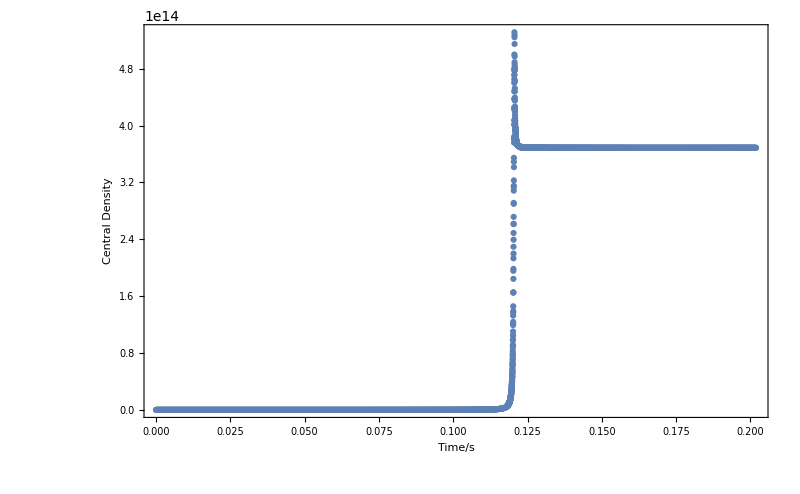

cdVSt.png

```mathematica
lstplt=ListPlot[data,Frame->True,ImageSize->imgSize,FrameLabel->{"Time/s","Central Density"}]
Export["cdVSt.png",lstplt]
```

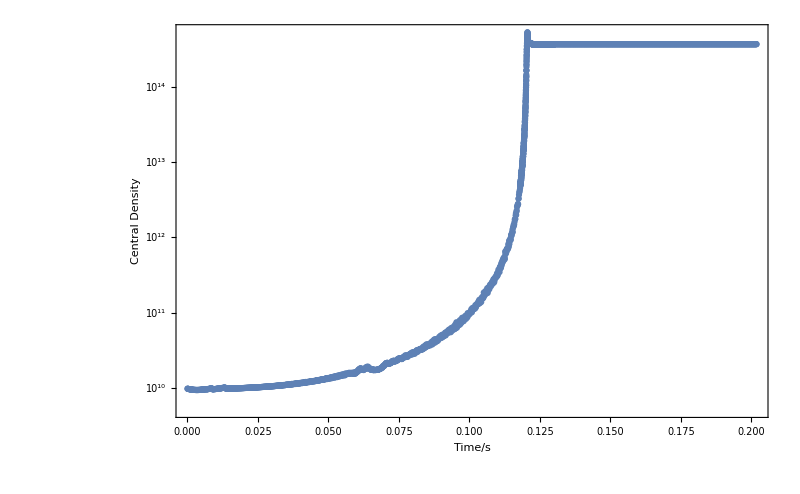

cdVStlog.png

```mathematica
ListLogPlot[data,Frame->True,ImageSize->imgSize,FrameLabel->{"Time/s","Central Density"}]
Export["cdVStlog.png",%]
```

### TIme scale

```mathematica
velData=Import["Data/v1.xg"]
```

"Time =    0.0000000000000000     
  -7.000000000E+04   7.274089645E+04
  -5.000000000E+04   5.322572305E+04
  -3.000000000E+04   3.371054966E+04
  -1.000000000E+04   1.419537626E+04
   1.000000000E+04  -1.419537626E+04
   3.000000000E+04  -3.37105…E+09   0.000000000E+00
   6.397512660E+09   0.000000000E+00
   6.454248292E+09   0.000000000E+00
   6.511487055E+09   0.000000000E+00
   6.569233410E+09   0.000000000E+00
   6.627491859E+09   0.000000000E+00
   6.686007484E+09   0.000000000E+00
  
  
 |  |  |  |

```mathematica
velDataCL=SemanticImport["Data/v1.xg"]
```

```mathematica
ListPlot[velDataCL]
```